```mathematica
update[x0_,y0_,z0_,k0_,l0_,phi0_]:=
{x0+1/k0*Tan[l0]*dphi,
y0+1/k0*(Cos[phi0+dphi]-Cos[phi0]),
z0+1/k0*(Sin[phi0+dphi]-Sin[phi0]),
k0,
l0,
phi0+dphi}
```

```mathematica
D[update[x,y,z,k,l,ϕ],{{x,y,z,k,l,ϕ}}]//MatrixForm
```

(1 | 0 | 0 | -(dphi Tan[l])/k^2 | (dphi Sec[l]^2)/k | 0
0 | 1 | 0 | -(-Cos[ϕ]+Cos[dphi+ϕ])/k^2 | 0 | (Sin[ϕ]-Sin[dphi+ϕ])/k
0 | 0 | 1 | -(-Sin[ϕ]+Sin[dphi+ϕ])/k^2 | 0 | (-Cos[ϕ]+Cos[dphi+ϕ])/k
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
updateWithTan[x0_,y0_,z0_,k0_,tanl0_,phi0_]:=
{x0+1/k0*tanl0*dphi,
y0+1/k0*(Cos[phi0+dphi]-Cos[phi0]),
z0+1/k0*(Sin[phi0+dphi]-Sin[phi0]),
k0,
tanl0,
phi0+dphi}
```

```mathematica
D[updateWithTan[x,y,z,k,tanl,ϕ],{{x,y,z,k,tanl,ϕ}}]//MatrixForm
```

(1 | 0 | 0 | -(dphi tanl)/k^2 | dphi/k | 0
0 | 1 | 0 | -(-Cos[ϕ]+Cos[dphi+ϕ])/k^2 | 0 | (Sin[ϕ]-Sin[dphi+ϕ])/k
0 | 0 | 1 | -(-Sin[ϕ]+Sin[dphi+ϕ])/k^2 | 0 | (-Cos[ϕ]+Cos[dphi+ϕ])/k
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

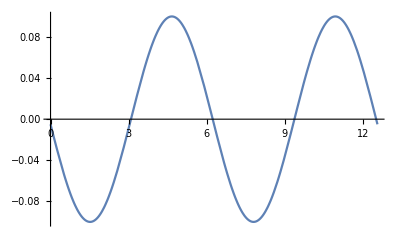

```mathematica
Plot[Cos[x+dx]-Cos[x]/.dx->0.1,{x,0,4Pi}]
```

```mathematica
updateCartesian[x_,y_,z_,px_,py_,pz_]:=
Flatten@Transpose[({{1, 0, 0, 1/m, 0, 0}, {0, 1, 0, 0, 1/m, 0}, {0, 0, 1, 0, 0, 1/m}, {0, 0, 0, 1, q/m*bz, -q/m*by}, {0, 0, 0, -q/m*bz, 1, q/m*bx}, {0, 0, 0, q/m*by, -q/m*bx, 1}}).({{x}, {y}, {z}, {px}, {py}, {pz}})+({{0}, {0}, {0}, {q ex}, {q ey}, {q ez}})]
```

```mathematica
updateCartesian[x,y,z,px,py,pz]
```

{px/m+x,py/m+y,pz/m+z,px+ex q+(bz py q)/m-(by pz q)/m,py+ey q-(bz px q)/m+(bx pz q)/m,pz+ez q+(by px q)/m-(bx py q)/m}

```mathematica
D[updateCartesian[x,y,z,px,py,pz],{{x,y,z,px,py,pz}}]//MatrixForm
```

(1 | 0 | 0 | 1/m | 0 | 0
0 | 1 | 0 | 0 | 1/m | 0
0 | 0 | 1 | 0 | 0 | 1/m
0 | 0 | 0 | 1 | (bz q)/m | -(by q)/m
0 | 0 | 0 | -(bz q)/m | 1 | (bx q)/m
0 | 0 | 0 | (by q)/m | -(bx q)/m | 1)

```mathematica
vel[px_,py_,pz_]=Solve[{px,py,pz}==1/Sqrt[1-Norm[{vx,vy,vz}]^2/c^2] m {vx,vy,vz},{vx,vy,vz}][[2]]
```

{vx→(c px)/(√(c^2 m^2+px^2+py^2+pz^2)),vy→(c py)/(√(c^2 m^2+px^2+py^2+pz^2)),vz→(c pz)/(√(c^2 m^2+px^2+py^2+pz^2))}

```mathematica
Clear[measure]
```

```mathematica
measure[x_,y_,z_,px_,py_,pz_]=FullSimplify[Flatten[{x,y,z,({vx,vy,vz}*pstep/Norm[{vx,vy,vz}])/.vel[px,py,pz]}],Assumptions->{Element[{px,py,pz,x,y,z},Reals],c>0,m>0,c^2 m^2+px^2+py^2+pz^2>0}]
```

{x,y,z,(pstep px)/(√(px^2+py^2+pz^2)),(pstep py)/(√(px^2+py^2+pz^2)),(pstep pz)/(√(px^2+py^2+pz^2))}

```mathematica
measure[1,2,1,10^-20,10^-20,0]/.pstep->10^-3.
```

{1,2,1,0.000707107,0.000707107,0}

```mathematica
measjac=D[measure[x,y,z,px,py,pz],{{x,y,z,px,py,pz}}];
measjac//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -(pstep px^2)/((px^2+py^2+pz^2)^(3/2))+pstep/(√(px^2+py^2+pz^2)) | -(pstep px py)/((px^2+py^2+pz^2)^(3/2)) | -(pstep px pz)/((px^2+py^2+pz^2)^(3/2))
0 | 0 | 0 | -(pstep px py)/((px^2+py^2+pz^2)^(3/2)) | -(pstep py^2)/((px^2+py^2+pz^2)^(3/2))+pstep/(√(px^2+py^2+pz^2)) | -(pstep py pz)/((px^2+py^2+pz^2)^(3/2))
0 | 0 | 0 | -(pstep px pz)/((px^2+py^2+pz^2)^(3/2)) | -(pstep py pz)/((px^2+py^2+pz^2)^(3/2)) | -(pstep pz^2)/((px^2+py^2+pz^2)^(3/2))+pstep/(√(px^2+py^2+pz^2)))

```mathematica
measjacStr=measjac//InputForm//ToString
```

{{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, -((pstep*px^2)/(px^2 + py^2 + pz^2)^(3/2)) + pstep/Sqrt[px^2 + py^2 + pz^2], -((pstep*px*py)/(px^2 + py^2 + pz^2)^(3/2)), -((pstep*px*pz)/(px^2 + py^2 + pz^2)^(3/2))}, {0, 0, 0, -((pstep*px*py)/(px^2 + py^2 + pz^2)^(3/2)), -((pstep*py^2)/(px^2 + py^2 + pz^2)^(3/2)) + pstep/Sqrt[px^2 + py^2 + pz^2], -((pstep*py*pz)/(px^2 + py^2 + pz^2)^(3/2))}, {0, 0, 0, -((pstep*px*pz)/(px^2 + py^2 + pz^2)^(3/2)), -((pstep*py*pz)/(px^2 + py^2 + pz^2)^(3/2)), -((pstep*pz^2)/(px^2 + py^2 + pz^2)^(3/2)) + pstep/Sqrt[px^2 + py^2 + pz^2]}}

```mathematica
pytrans={"["->"(","]"->")","{"->"[","}"->"]","Sqrt"->"sqrt","pstep"->"pos_step","^"->"**"}
```

{[→(,]→),{→[,}→],Sqrt→sqrt,pstep→pos_step,^→**}

```mathematica
StringReplace[measjac,pytrans]
```

[[1, 0, 0, 0, 0, 0], [0, 1, 0, 0, 0, 0], [0, 0, 1, 0, 0, 0], [0, 0, 0, -((pos_step*px**2)/(px**2 + py**2 + pz**2)**(3/2)) + pos_step/sqrt(px**2 + py**2 + pz**2), -((pos_step*px*py)/(px**2 + py**2 + pz**2)**(3/2)), -((pos_step*px*pz)/(px**2 + py**2 + pz**2)**(3/2))], [0, 0, 0, -((pos_step*px*py)/(px**2 + py**2 + pz**2)**(3/2)), -((pos_step*py**2)/(px**2 + py**2 + pz**2)**(3/2)) + pos_step/sqrt(px**2 + py**2 + pz**2), -((pos_step*py*pz)/(px**2 + py**2 + pz**2)**(3/2))], [0, 0, 0, -((pos_step*px*pz)/(px**2 + py**2 + pz**2)**(3/2)), -((pos_step*py*pz)/(px**2 + py**2 + pz**2)**(3/2)), -((pos_step*pz**2)/(px**2 + py**2 + pz**2)**(3/2)) + pos_step/sqrt(px**2 + py**2 + pz**2)]]

```mathematica
measjac/.{px->10.^-20,py->10.^-20,pz->10.^-20,pstep->1 10^-3}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 3.849×10^16 | -1.9245×10^16 | -1.9245×10^16
0 | 0 | 0 | -1.9245×10^16 | 3.849×10^16 | -1.9245×10^16
0 | 0 | 0 | -1.9245×10^16 | -1.9245×10^16 | 3.849×10^16)

```mathematica
Sqrt[(8 10^6)^2-(4*980 10^6)^2]
```

8000000 ⅈ √240099

```mathematica
Solve[k==Sqrt[p^2+mc2^2]-mc2,p]/.{k->8. 10^6,mc2->980. 10^6}
```

{{p→-1.25475×10^8},{p→1.25475×10^8}}

```mathematica
1.3 10^8/10^6*1.6 10^-19
```

2.08×10^-17